# Mathematical generation of data - driven hippocampal CA1 pyramidal neurons and interneurons copies via A - GLIF models for large - scale networks covering the experimental variability range

## A . Marasco, C . Tribuzi, A. Iuorio and M . Migliore

### Instructions

Get . zip of JSON file from the repository, unzip them and locate them in the working directory together with this notebook.

```mathematica
filepath=NotebookDirectory[];
```

### Dataset creation

```mathematica
creaDatasetSpikeISI[dbNeu_,type_]:=Module[{neuroni,datasetOut,correnti,valoriTmp,valori,isi,setDiValori},
correnti={"200","400","600","800","1000"};
neuroni=Keys@dbNeu;

datasetOut=
<|Table[
neurone-><|Table[
valoriTmp=If[type=="exp",ToExpression[dbNeu[neurone]["spike_times_exp"][corr]],ToExpression[dbNeu[neurone]["spike_times_sim"][corr]]];
(* se valoriTmp == Null*)
If[valoriTmp==Null,valori = 0,If[type=="exp",valori=valoriTmp-31.2,valori=valoriTmp]];
(* se valoriTmp == {Null}*)
If[valoriTmp=={Null},valori = 0,If[type=="exp",valori=valoriTmp-31.2,valori=valoriTmp]];
If[Length@valori>1,
	isi=Table[valori[[i+1]]-valori[[i]],{i,Length@valori-1}];,
	If[
	Length@valori==1,isi =valori,
	isi={0};];
valori=0];

<|
corr<>" - time1stSpike"->If[Length@valori<1,0,Min[valori]],
corr<>" - timeLastSpike"->If[Length@valori<1,0,Max[valori]],
corr<>" - spikeNumber"->Length[valori],
corr<> " - ISImin"-> If[NumberQ@isi[[1]],Min[isi],Missing[]],
corr<> " - ISImax"-> If[NumberQ@isi[[1]],Max[isi],Missing[]],
corr<> " - ISImean"-> If[NumberQ@isi[[1]],Mean[isi],Missing[]],
corr<> " - ISIstd"-> If[Length[isi]<2,Missing[],StandardDeviation[isi]]
|>,
{corr,correnti}]|>,
{neurone,neuroni}]|>;

(*Print[datasetOut]*);
Return[datasetOut]]
```

#### Piramidali

```mathematica
filename = "expNeuronDB_V006small_piramidali_dati_2023_06_15";
dbNeuPyrOrig=Import[filepath<>"\\"<>filename<>".json","RawJSON"];
```

```mathematica
datasetPyr=creaDatasetSpikeISI[dbNeuPyrOrig,"exp"];
```

```mathematica
datasetPyr[[3]]
```

<|200 - time1stSpike→0,200 - timeLastSpike→0,200 - spikeNumber→0,200 - ISImin→0,200 - ISImax→0,200 - ISImean→0,200 - ISIstd→Missing[],400 - time1stSpike→0,400 - timeLastSpike→0,400 - spikeNumber→0,400 - ISImin→0,400 - ISImax→0,400 - ISImean→0,400 - ISIstd→Missing[],600 - time1stSpike→0,600 - timeLastSpike→0,600 - spikeNumber→0,600 - ISImin→0,600 - ISImax→0,600 - ISImean→0,600 - ISIstd→Missing[],800 - time1stSpike→43.9,800 - timeLastSpike→398.5,800 - spikeNumber→4,800 - ISImin→44.4,800 - ISImax→230.8,800 - ISImean→118.2,800 - ISIstd→99.0723,1000 - time1stSpike→22.1,1000 - timeLastSpike→190.,1000 - spikeNumber→5,1000 - ISImin→17.7,1000 - ISImax→75.7,1000 - ISImean→41.975,1000 - ISIstd→25.029|>

```mathematica
Values@datasetPyr[[3]]
```

{0,0,0,0,0,0,Missing[],0,0,0,0,0,0,Missing[],0,0,0,0,0,0,Missing[],43.9,398.5,4,44.4,230.8,118.2,99.0723,22.1,190.,5,17.7,75.7,41.975,25.029}

#### Interneuroni

```mathematica
filename = "expNeuronDB_V006small_interneuroni_dati_2022_07_15";
dbNeuIntOrig=Import[filepath<>"\\"<>filename<>".json","RawJSON"];
```

```mathematica
datasetInt=creaDatasetSpikeISI[dbNeuIntOrig,"exp"];
```

```mathematica
datasetInt[[3]]
```

<|200 - time1stSpike→0,200 - timeLastSpike→0,200 - spikeNumber→0,200 - ISImin→0,200 - ISImax→0,200 - ISImean→0,200 - ISIstd→Missing[],400 - time1stSpike→16.,400 - timeLastSpike→134.6,400 - spikeNumber→11,400 - ISImin→3.5,400 - ISImax→23.2,400 - ISImean→11.86,400 - ISIstd→6.12322,600 - time1stSpike→1.6,600 - timeLastSpike→210.6,600 - spikeNumber→17,600 - ISImin→6.1,600 - ISImax→23.3,600 - ISImean→13.0625,600 - ISIstd→5.03546,800 - time1stSpike→6.2,800 - timeLastSpike→398.7,800 - spikeNumber→21,800 - ISImin→5.7,800 - ISImax→110.7,800 - ISImean→19.625,800 - ISIstd→26.5882,1000 - time1stSpike→3.7,1000 - timeLastSpike→329.2,1000 - spikeNumber→29,1000 - ISImin→4.2,1000 - ISImax→35.7,1000 - ISImean→11.625,1000 - ISIstd→6.96747|>

```mathematica
filename = "neuronOriginalNeuronsDB_V006small_par_2023_06_15_int";
dbNeuIntOrig=Import[filepath<>"\\"<>filename<>".json","RawJSON"];
```

```mathematica
datasetIntSim=creaDatasetSpikeISI[dbNeuIntOrig,"sim"];
```

```mathematica
datasetIntSim[[7]]
```

<|200 - time1stSpike→0,200 - timeLastSpike→0,200 - spikeNumber→0,200 - ISImin→0,200 - ISImax→0,200 - ISImean→0,200 - ISIstd→Missing[],400 - time1stSpike→15.2,400 - timeLastSpike→29.2,400 - spikeNumber→3,400 - ISImin→6.,400 - ISImax→8.,400 - ISImean→7.,400 - ISIstd→1.41421,600 - time1stSpike→7.6,600 - timeLastSpike→252.8,600 - spikeNumber→14,600 - ISImin→3.8,600 - ISImax→31.2,600 - ISImean→18.8615,600 - ISIstd→10.4024,800 - time1stSpike→5.,800 - timeLastSpike→380.6,800 - spikeNumber→18,800 - ISImin→3.2,800 - ISImax→34.6,800 - ISImean→22.0941,800 - ISIstd→12.051,1000 - time1stSpike→3.8,1000 - timeLastSpike→355.4,1000 - spikeNumber→17,1000 - ISImin→3.,1000 - ISImax→36.,1000 - ISImean→21.975,1000 - ISIstd→13.0034|>

```mathematica
Length@datasetIntSim
```

24

### Functions for classification

```mathematica
classificaCopie[dbcopie01_,myClassifier_]:=Module[{datasetPyrCopie01b,indexNotNullRows,datasetPyrCopie01bCleaned,classificazioneCopie01b,a1,meanProbA1,stdProbA1,probaInt,probaPyr},
datasetPyrCopie01b=creaDatasetSpikeISI[dbcopie01,"sim"];
(* delete empty rows*)
indexNotNullRows={};
Table[If[Total@DeleteCases[Values@datasetPyrCopie01b[[i]],Missing[]]!=0,AppendTo[indexNotNullRows,i]],{i,Length@datasetPyrCopie01b}];
datasetPyrCopie01bCleaned=datasetPyrCopie01b[[indexNotNullRows]];
classificazioneCopie01b=Table[myClassifier[datasetPyrCopie01bCleaned[[i]],{"Probabilities","Decision"}],{i,Length@datasetPyrCopie01bCleaned}];a1=Counts[classificazioneCopie01b[[All,2]]];
probaPyr=Table[classificazioneCopie01b[[i,1]]["pyr"],{i,Length@datasetPyrCopie01bCleaned}];
probaInt=Table[classificazioneCopie01b[[i,1]]["int"],{i,Length@datasetPyrCopie01bCleaned}];
meanProbA1=<|
"pyr"->Mean[probaPyr],"int"->Mean[probaInt]
|>;
stdProbA1=<|
"pyr"->StandardDeviation[probaPyr],"int"->StandardDeviation[probaInt]
|>;
Return[{probaPyr,probaInt,Length@indexNotNullRows,a1,meanProbA1,stdProbA1}]
]
```

```mathematica
classificaCopieEtichette[dbcopie01_,myClassifier_]:=Module[{datasetPyrCopie01b,indexNotNullRows,datasetPyrCopie01bCleaned,classificazioneCopie01b,a1,meanProbA1,stdProbA1,probaInt,probaPyr},
datasetPyrCopie01b=creaDatasetSpikeISI[dbcopie01,"sim"];
(* delete empty rows*)
indexNotNullRows={};
Table[If[Total@DeleteCases[Values@datasetPyrCopie01b[[i]],Missing[]]!=0,AppendTo[indexNotNullRows,i]],{i,Length@datasetPyrCopie01b}];
datasetPyrCopie01bCleaned=datasetPyrCopie01b[[indexNotNullRows]];
classificazioneCopie01b=Table[myClassifier[datasetPyrCopie01bCleaned[[i]],{"Probabilities","Decision"}],{i,Length@datasetPyrCopie01bCleaned}];a1=Counts[classificazioneCopie01b[[All,2]]];
probaPyr=Table[classificazioneCopie01b[[i,1]]["pyr"],{i,Length@datasetPyrCopie01bCleaned}];
probaInt=Table[classificazioneCopie01b[[i,1]]["int"],{i,Length@datasetPyrCopie01bCleaned}];
meanProbA1=<|
"pyr"->Mean[probaPyr],"int"->Mean[probaInt]
|>;
stdProbA1=<|
"pyr"->StandardDeviation[probaPyr],"int"->StandardDeviation[probaInt]
|>;
Return[{Keys@datasetPyrCopie01bCleaned,probaPyr,probaInt,Length@indexNotNullRows,a1,meanProbA1,stdProbA1}]
]
```

## Classifier

#### GBT - exp+sim

```mathematica
trainigPyr=Table[datasetPyr[[i]]->"pyr",{i,Length[datasetPyr]}];
trainigInt=Table[datasetInt[[i]]->"int",{i,Length@datasetInt}];
trainigIntSim=Table[datasetIntSim[[i]]->"int",{i,Length@datasetIntSim}];
```

```mathematica
trainingSet=Flatten@{trainigPyr,trainigInt,trainigIntSim};
```

```mathematica
trainingSet[[60]]
```

<|200 - time1stSpike→3.5,200 - timeLastSpike→249.8,200 - spikeNumber→11,200 - ISImin→9.4,200 - ISImax→67.4,200 - ISImean→24.63,200 - ISIstd→20.0346,400 - time1stSpike→2.6,400 - timeLastSpike→108.2,400 - spikeNumber→8,400 - ISImin→7.1,400 - ISImax→25.3,400 - ISImean→15.0857,400 - ISIstd→6.51778,600 - time1stSpike→3.9,600 - timeLastSpike→367.3,600 - spikeNumber→12,600 - ISImin→12.5,600 - ISImax→68.6,600 - ISImean→33.0364,600 - ISIstd→21.7311,800 - time1stSpike→5.9,800 - timeLastSpike→289.4,800 - spikeNumber→22,800 - ISImin→4.5,800 - ISImax→42.9,800 - ISImean→13.5,800 - ISIstd→9.59333,1000 - time1stSpike→3.4,1000 - timeLastSpike→320.9,1000 - spikeNumber→29,1000 - ISImin→4.1,1000 - ISImax→24.4,1000 - ISImean→11.3393,1000 - ISIstd→5.07144|>→int

```mathematica
myClassifier01=Classify[trainingSet,Method->"GradientBoostedTrees"]
```

ClassifierFunction[…]

```mathematica
Information[myClassifier01 ]
```

Classifier information
Data type | Mixed (number: 35)
Classes | ,,intpyr
Accuracy | (98.4.) %
Method | GradientBoostedTrees
Single evaluation time | 6.27 ms/example
Batch evaluation speed | 21.1 examples/ms
Loss | 0.079 ± 0.054
Model memory | 671. kB
Training examples used | 108 examples
Training time | 3.51 s
 |

```mathematica
Count[Table[myClassifier01[datasetPyr[[i]]],{i,Length@datasetPyr}],"pyr"]
Count[Table[myClassifier01[datasetInt[[i]]],{i,Length@datasetInt}],"int"]
Count[Table[myClassifier01[datasetIntSim[[i]]],{i,Length@datasetIntSim}],"int"]
```

58

26

24

```mathematica
Table[myClassifier01[datasetIntSim[[i]]],{i,Length@datasetIntSim}]
```

{int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int}

```mathematica
Table[myClassifier01[Values@datasetIntSim[[i]]],{i,Length@datasetIntSim}]
```

{int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int,int}

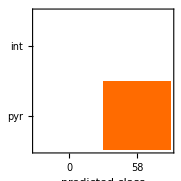
{1.,-Graphics-}

```mathematica
cm=ClassifierMeasurements[myClassifier01,trainigPyr,{"Accuracy","ConfusionMatrixPlot"}]
```

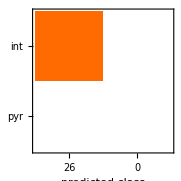
{1.,-Graphics-}

```mathematica
ClassifierMeasurements[myClassifier01,trainigInt,{"Accuracy","ConfusionMatrixPlot"}]
```

```mathematica
datasetInt[[1]]
```

<|200 - time1stSpike→0,200 - timeLastSpike→0,200 - spikeNumber→0,200 - ISImin→0,200 - ISImax→0,200 - ISImean→0,200 - ISIstd→Missing[],400 - time1stSpike→0.4,400 - timeLastSpike→323.2,400 - spikeNumber→4,400 - ISImin→96.4,400 - ISImax→117.2,400 - ISImean→107.6,400 - ISIstd→10.4919,600 - time1stSpike→0.5,600 - timeLastSpike→353.9,600 - spikeNumber→5,600 - ISImin→18.2,600 - ISImax→176.9,600 - ISImean→88.35,600 - ISIstd→71.9505,800 - time1stSpike→0.4,800 - timeLastSpike→141.3,800 - spikeNumber→6,800 - ISImin→6.5,800 - ISImax→44.7,800 - ISImean→28.18,800 - ISIstd→15.8103,1000 - time1stSpike→0.4,1000 - timeLastSpike→298.7,1000 - spikeNumber→8,1000 - ISImin→4.6,1000 - ISImax→194.2,1000 - ISImean→42.6143,1000 - ISIstd→68.0176|>

```mathematica
myClassifier01[datasetInt[[1]],"Probabilities"]
```

<|int→0.97055,pyr→0.0294496|>

<|int→0.97055,pyr→0.0294496|>

<|int→0.97055,pyr→0.0294496|>

«1 more identical outputs»

## Classification

### Copies - 01(trance a)

```mathematica
filename = "neuronCopiesDatabase_pyr_2023_10_16_a";
dbcopie02=Import[filepath<>"\\"<>filename<>".json","RawJSON"];
```

```mathematica
Length@Keys@dbcopie02
```

256655

#### Labels

```mathematica
res=classificaCopieEtichette[dbcopie02[[;;10]],myClassifier01]
```

{{95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_-10_0_0_0_p_1,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_-10_0_0_25_p_1,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_-10_0_25_0_p_1,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_-10_0_25_25_p_1,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_0_0_0_0_p_1,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_0_0_0_25_p_1,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_0_0_25_0_p_1,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_0_0_25_25_p_1,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_0_-10_0_0_0_p_1,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_0_-10_0_0_25_p_1},{0.987642,0.987642,0.991403,0.987642,0.987642,0.987642,0.991403,0.987642,0.987642,0.987642},{0.0123581,0.0123581,0.00859717,0.0123581,0.0123581,0.0123581,0.00859717,0.0123581,0.0123581,0.0123581},10,<|pyr→10|>,<|pyr→0.988394,int→0.0116059|>,<|pyr→0.00158575,int→0.00158575|>}

```mathematica
resAss=Association@Thread[res[[1]]->res[[2]]]
```

<|95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_-10_0_0_0_p_1→0.987642,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_-10_0_0_25_p_1→0.987642,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_-10_0_25_0_p_1→0.991403,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_-10_0_25_25_p_1→0.987642,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_0_0_0_0_p_1→0.987642,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_0_0_0_25_p_1→0.987642,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_0_0_25_0_p_1→0.991403,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_0_0_25_25_p_1→0.987642,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_0_-10_0_0_0_p_1→0.987642,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_0_-10_0_0_25_p_1→0.987642|>

```mathematica
Select[resAss,#>0.988&]
```

<|95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_-10_0_25_0_p_1→0.991403,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_0_0_25_0_p_1→0.991403|>

```mathematica
probPyrAtmp={};
probIntAtmp={};
nRighe=4;
Do[
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*i;;i+nRighe*i+nRighe]],myClassifier01];
AppendTo[probPyrAtmp,Thread[nomi->probPyr]];
AppendTo[probIntAtmp,Thread[nomi->probInt]];
,{i,0,6}];
```

```mathematica
Association@Flatten[probIntAtmp]
```

<|95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_-10_0_0_0_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_-10_0_0_25_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_-10_0_25_0_p_1→0.00859717,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_-10_0_25_25_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_0_0_0_0_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_0_0_0_25_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_0_0_25_0_p_1→0.00859717,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_-25_0_0_25_25_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_0_-10_0_0_0_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_0_-10_0_0_25_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_0_-10_0_25_0_p_1→0.00859717,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_0_-10_0_25_25_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_0_0_0_0_0_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_0_0_0_0_25_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_0_0_0_25_0_p_1→0.00859717,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.5_R_0_0_0_0_25_25_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.75_R_0_-25_-10_0_0_0_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.75_R_0_-25_-10_0_0_25_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.75_R_0_-25_-10_0_25_0_p_1→0.00859717,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.75_R_0_-25_-10_0_25_25_p_1→0.00859717,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.75_R_0_-25_0_0_0_0_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.75_R_0_-25_0_0_0_25_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.75_R_0_-25_0_0_25_0_p_1→0.00859717,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.75_R_0_-25_0_0_25_25_p_1→0.00859717,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.75_R_0_0_-10_0_0_0_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.75_R_0_0_-10_0_0_25_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.75_R_0_0_-10_0_25_0_p_1→0.00859717,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.75_R_0_0_-10_0_25_25_p_1→0.00859717,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.75_R_0_0_0_0_0_0_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.75_R_0_0_0_0_0_25_p_1→0.0123581,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.75_R_0_0_0_0_25_0_p_1→0.00859717,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_0.75_R_0_0_0_0_25_25_p_1→0.00859717,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_1.5_R_0_-25_-10_0_0_0_p_1→0.00859717,95810005_iadap_0.1_Idep_0.75_Idep0_0.25_c_0.75_d_1.5_R_0_-25_-10_0_0_25_p_1→0.0123581|>

#### Classification using labels

```mathematica
probPyrAtmp={};
probIntAtmp={};
nRighe=40000;
Do[
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*i;;i+nRighe*i+nRighe]],myClassifier01];
AppendTo[probPyrAtmp,Thread[nomi->probPyr]];
AppendTo[probIntAtmp,Thread[nomi->probInt]];
,{i,0,2}];
```

```mathematica
Length@Association@Flatten@probPyrAtmp
```

115225

```mathematica
nRighe*5
```

200000

```mathematica
Do[
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*i;;i+nRighe*i+nRighe]],myClassifier01];
AppendTo[probPyrAtmp,Thread[nomi->probPyr]];
AppendTo[probIntAtmp,Thread[nomi->probInt]];
,{i,3,5}];
```

```mathematica
Length@Association@Flatten@probPyrAtmp
```

233816

```mathematica
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*6;;]],myClassifier01];
AppendTo[probPyrAtmp,Thread[nomi->probPyr]];
AppendTo[probIntAtmp,Thread[nomi->probInt]];
```

```mathematica
Length@Association@Flatten@probPyrAtmp
```

250466

```mathematica
probPyrAtmp[[1]]
```

```mathematica
classificatiComeInterneuroniAtmp=Length@Select[Association@Flatten[probIntAtmp],#>0.5&]
```

3813

```mathematica
classificatiComePiramidaliAtmp=Length@Select[Association@Flatten[probPyrAtmp],#>0.5&]
```

246653

```mathematica
accuratezzaA=N@classificatiComePiramidaliAtmp/(classificatiComePiramidaliAtmp+classificatiComeInterneuroniAtmp)
```

0.984776

```mathematica
mediaPYRPyrA=Mean[Select[Association@Flatten[probPyrAtmp],#>0.5&]]
```

0.94132

### Copies - 01(trance b)

```mathematica
filename = "neuronCopiesDatabase_pyr_2023_10_16_b";
dbcopie02=Import[filepath<>"\\"<>filename<>".json","RawJSON"];
```

```mathematica
Length@Keys@dbcopie02
```

178425

#### Classification using labels

```mathematica
probPyrBtmp={};
probIntBtmp={};
nRighe=40000;
Do[
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*i;;i+nRighe*i+nRighe]],myClassifier01];
AppendTo[probPyrBtmp,Thread[nomi->probPyr]];
AppendTo[probIntBtmp,Thread[nomi->probInt]];
,{i,0,2}];
```

```mathematica
Length@Association@Flatten@probPyrBtmp
```

120002

```mathematica
Do[
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*i;;i+nRighe*i+nRighe]],myClassifier01];
AppendTo[probPyrBtmp,Thread[nomi->probPyr]];
AppendTo[probIntBtmp,Thread[nomi->probInt]];
,{i,3,4}];
```

Part::take: Cannot take positions 160001 through 200004 in Association[<<1421006232 bytes>>].

Keys::invrl: The argument <<1421006376 bytes>>[[]] is not a valid Association or a list of rules.

Table::iterb: Iterator {<<1452737488 bytes>>} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Values::invrl: The argument Table[<<4358218568 bytes>>] is not a valid Association or a list of rules.

StandardDeviation::shlen: The argument {} should have at least two elements.

```mathematica
Length@Association@Flatten@probPyrBtmp
```

156635

```mathematica
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*5;;]],myClassifier01];
AppendTo[probPyrBtmp,Thread[nomi->probPyr]];
AppendTo[probIntBtmp,Thread[nomi->probInt]];
```

Part::take: Cannot take positions 200001 through -1 in Association[<<1452737240 bytes>>].

Keys::invrl: The argument <<1452737368 bytes>>[[]] is not a valid Association or a list of rules.

Table::iterb: Iterator {<<1452737472 bytes>>} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Values::invrl: The argument Table[<<4358218520 bytes>>] is not a valid Association or a list of rules.

StandardDeviation::shlen: The argument {} should have at least two elements.

```mathematica
Length@Association@Flatten@probPyrBtmp
```

156635

```mathematica
classificatiComeInterneuroniBtmp=Length@Select[Association@Flatten[probIntBtmp],#>0.5&]
```

8011

```mathematica
classificatiComePiramidaliBtmp=Length@Select[Association@Flatten[probPyrBtmp],#>0.5&]
```

148624

```mathematica
accuratezzaB=N@classificatiComePiramidaliBtmp/(classificatiComePiramidaliBtmp+classificatiComeInterneuroniBtmp)
```

0.948856

```mathematica
mediaPYRPyrB=Mean[Select[Association@Flatten[probPyrBtmp],#>0.5&]]
```

0.974086

### Copies - 01(trance c)

```mathematica
filename = "neuronCopiesDatabase_pyr_2023_10_16_c";
dbcopie02=Import[filepath<>"\\"<>filename<>".json","RawJSON"];
```

```mathematica
Length@Keys@dbcopie02
```

81081

#### Classification using labels

```mathematica
probPyrCtmp={};
probIntCtmp={};
nRighe=40000;
Do[
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*i;;i+nRighe*i+nRighe]],myClassifier01];
AppendTo[probPyrCtmp,Thread[nomi->probPyr]];
AppendTo[probIntCtmp,Thread[nomi->probInt]];
,{i,0,1}];
```

```mathematica
Length@Association@Flatten@probPyrCtmp
```

80001

```mathematica
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*2;;]],myClassifier01];
AppendTo[probPyrCtmp,Thread[nomi->probPyr]];
AppendTo[probIntCtmp,Thread[nomi->probInt]];
```

```mathematica
Length@Association@Flatten@probPyrCtmp
```

81081

```mathematica
classificatiComeInterneuroniCtmp=Length@Select[Association@Flatten[probIntCtmp],#>0.5&]
```

1852

```mathematica
classificatiComePiramidaliCtmp=Length@Select[Association@Flatten[probPyrCtmp],#>0.5&]
```

79229

```mathematica
accuratezzaC=N@classificatiComePiramidaliCtmp/(classificatiComePiramidaliCtmp+classificatiComeInterneuroniCtmp)
```

0.977159

```mathematica
mediaPYRPyrC=Mean[Select[Association@Flatten[probPyrCtmp],#>0.5&]]
```

0.967408

### Copies - 01(trance d)

```mathematica
filename = "neuronCopiesDatabase_pyr_2023_10_16_d";
dbcopie02=Import[filepath<>"\\"<>filename<>".json","RawJSON"];
```

```mathematica
Length@Keys@dbcopie02
```

149498

#### Classification using labels

```mathematica
probPyrDtmp={};
probIntDtmp={};
nRighe=40000;
Do[
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*i;;i+nRighe*i+nRighe]],myClassifier01];
AppendTo[probPyrDtmp,Thread[nomi->probPyr]];
AppendTo[probIntDtmp,Thread[nomi->probInt]];
,{i,0,2}];
```

```mathematica
Length@Association@Flatten@probPyrDtmp
```

109348

```mathematica
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*3;;]],myClassifier01];
AppendTo[probPyrDtmp,Thread[nomi->probPyr]];
AppendTo[probIntDtmp,Thread[nomi->probInt]];
```

```mathematica
Length@Association@Flatten@probPyrDtmp
```

138844

```mathematica
classificatiComeInterneuroniDtmp=Length@Select[Association@Flatten[probIntDtmp],#>0.5&]
```

25855

```mathematica
classificatiComePiramidaliDtmp=Length@Select[Association@Flatten[probPyrDtmp],#>0.5&]
```

112989

```mathematica
accuratezzaD=N@classificatiComePiramidaliDtmp/(classificatiComePiramidaliDtmp+classificatiComeInterneuroniDtmp)
```

0.813784

```mathematica
mediaPYRPyrD=Mean[Select[Association@Flatten[probPyrDtmp],#>0.5&]]
```

0.931936

### Copies - 01(trance e)

```mathematica
filename = "neuronCopiesDatabase_pyr_2023_10_16_e";
dbcopie02=Import[filepath<>"\\"<>filename<>".json","RawJSON"];
```

```mathematica
Length@Keys@dbcopie02
```

136686

#### Classification using labels

```mathematica
probPyrEtmp={};
probIntRtmp={};
nRighe=40000;
Do[
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*i;;i+nRighe*i+nRighe]],myClassifier01];
AppendTo[probPyrEtmp,Thread[nomi->probPyr]];
AppendTo[probIntRtmp,Thread[nomi->probInt]];
,{i,0,2}];
```

```mathematica
Length@Association@Flatten@probPyrEtmp
```

119986

```mathematica
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*3;;]],myClassifier01];
AppendTo[probPyrEtmp,Thread[nomi->probPyr]];
AppendTo[probIntRtmp,Thread[nomi->probInt]];
```

```mathematica
Length@Association@Flatten@probPyrEtmp
```

136410

```mathematica
classificatiComeInterneuroniEtmp=Length@Select[Association@Flatten[probIntRtmp],#>0.5&]
```

5928

```mathematica
classificatiComePiramidaliEtmp=Length@Select[Association@Flatten[probPyrEtmp],#>0.5&]
```

130482

```mathematica
accuratezzaE=N@classificatiComePiramidaliEtmp/(classificatiComePiramidaliEtmp+classificatiComeInterneuroniEtmp)
```

0.956543

```mathematica
mediaPYRPyrE=Mean[Select[Association@Flatten[probPyrEtmp],#>0.5&]]
```

0.965718

```mathematica
probIntEtmp=probIntRtmp;
```

### Copies - 01(trance f)

```mathematica
filename = "neuronCopiesDatabase_pyr_2023_10_16_f";
dbcopie02=Import[filepath<>"\\"<>filename<>".json","RawJSON"];
```

```mathematica
Length@Keys@dbcopie02
```

100717

#### Classification using labels

```mathematica
probPyrFtmp={};
probIntFtmp={};
nRighe=40000;
Do[
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*i;;i+nRighe*i+nRighe]],myClassifier01];
AppendTo[probPyrFtmp,Thread[nomi->probPyr]];
AppendTo[probIntFtmp,Thread[nomi->probInt]];
,{i,0,1}];
```

```mathematica
Length@Association@Flatten@probPyrFtmp
```

79921

```mathematica
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*2;;]],myClassifier01];
AppendTo[probPyrFtmp,Thread[nomi->probPyr]];
AppendTo[probIntFtmp,Thread[nomi->probInt]];
```

```mathematica
Length@Association@Flatten@probPyrFtmp
```

100637

```mathematica
classificatiComeInterneuroniFtmp=Length@Select[Association@Flatten[probIntFtmp],#>0.5&]
```

22139

```mathematica
classificatiComePiramidaliFtmp=Length@Select[Association@Flatten[probPyrFtmp],#>0.5&]
```

78498

```mathematica
accuratezzaF=N@classificatiComePiramidaliFtmp/(classificatiComePiramidaliFtmp+classificatiComeInterneuroniFtmp)
```

0.780011

```mathematica
mediaPYRPyrF=Mean[Select[Association@Flatten[probPyrFtmp],#>0.5&]]
```

0.929186

### Copies - 01(trance g)

```mathematica
filename = "neuronCopiesDatabase_pyr_2023_10_16_g";
dbcopie02=Import[filepath<>"\\"<>filename<>".json","RawJSON"];
```

```mathematica
Length@Keys@dbcopie02
```

240368

#### Classification using labels

```mathematica
probPyrGtmp={};
probIntGtmp={};
nRighe=40000;
Do[
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*i;;i+nRighe*i+nRighe]],myClassifier01];
AppendTo[probPyrGtmp,Thread[nomi->probPyr]];
AppendTo[probIntGtmp,Thread[nomi->probInt]];
,{i,0,2}];
```

```mathematica
Length@Association@Flatten@probPyrGtmp
```

114551

```mathematica
classificatiComeInterneuroniGtmp=Length@Select[Association@Flatten[probIntGtmp],#>0.5&]
```

6552

```mathematica
classificatiComePiramidaliGtmp=Length@Select[Association@Flatten[probPyrGtmp],#>0.5&]
```

107999

```mathematica
accuratezzaG=N@classificatiComePiramidaliGtmp/(classificatiComePiramidaliGtmp+classificatiComeInterneuroniGtmp)
```

0.942803

```mathematica
mediaPYRPyrG=Mean[Select[Association@Flatten[probPyrGtmp],#>0.5&]]
```

0.965922

```mathematica
probPyrGtmp={};
probIntGtmp={};
nRighe=40000;
Do[
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*i;;i+nRighe*i+nRighe]],myClassifier01];
AppendTo[probPyrGtmp,Thread[nomi->probPyr]];
AppendTo[probIntGtmp,Thread[nomi->probInt]];
,{i,3,5}];
```

```mathematica
Length@Association@Flatten@probPyrGtmp
```

120005

```mathematica
classificatiComeInterneuroniGtmp=Length@Select[Association@Flatten[probIntGtmp],#>0.5&]
```

788

```mathematica
classificatiComePiramidaliGtmp=Length@Select[Association@Flatten[probPyrGtmp],#>0.5&]
```

119217

```mathematica
accuratezzaG=N@classificatiComePiramidaliGtmp/(classificatiComePiramidaliGtmp+classificatiComeInterneuroniGtmp)
```

0.993434

```mathematica
mediaPYRPyrG=Mean[Select[Association@Flatten[probPyrGtmp],#>0.5&]]
```

0.981116

```mathematica
probPyrGtmp={};
probIntGtmp={};
nRighe=40000;
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*6;;]],myClassifier01];
AppendTo[probPyrGtmp,Thread[nomi->probPyr]];
AppendTo[probIntGtmp,Thread[nomi->probInt]];
```

```mathematica
Length@Association@Flatten@probPyrGtmp
```

368

```mathematica
classificatiComeInterneuroniGtmp=Length@Select[Association@Flatten[probIntGtmp],#>0.5&]
```

0

```mathematica
classificatiComePiramidaliGtmp=Length@Select[Association@Flatten[probPyrGtmp],#>0.5&]
```

368

```mathematica
accuratezzaG=N@classificatiComePiramidaliGtmp/(classificatiComePiramidaliGtmp+classificatiComeInterneuroniGtmp)
```

1.

```mathematica
mediaPYRPyrG=Mean[Select[Association@Flatten[probPyrGtmp],#>0.5&]]
```

0.986133

### Copies interneurons - bAC

```mathematica
filename = "neuronCopiesDatabase_intern_2023_07_10_bAC";
dbcopie02=Import[filepath<>"\\"<>filename<>".json","RawJSON"];
```

```mathematica
Length@Keys@dbcopie02
```

45192

#### Classification using labels

```mathematica
probPyrBAC={};
probIntBAC={};
nRighe=10000;
Do[
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*i;;i+nRighe*i+nRighe]],myClassifier01];
AppendTo[probPyrBAC,Thread[nomi->probPyr]];
AppendTo[probIntBAC,Thread[nomi->probInt]];
,{i,0,3}];
```

```mathematica
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*4;;]],myClassifier01];
AppendTo[probPyrBAC,Thread[nomi->probPyr]];
AppendTo[probIntBAC,Thread[nomi->probInt]];
```

```mathematica
Length@Association@Flatten@probIntBAC
```

45192

```mathematica
classificatiComeInterneuroniBAC=Length@Select[Association@Flatten[probIntBAC],#>0.5&]
```

26076

```mathematica
classificatiComePiramidaliBAC=Length@Select[Association@Flatten[probPyrBAC],#>0.5&]
```

19116

```mathematica
accuratezzaBAC=N@classificatiComeInterneuroniBAC/(classificatiComePiramidaliBAC+classificatiComeInterneuroniBAC)
```

0.577005

```mathematica
mediaINTint=Mean[Select[Association@Flatten[probIntBAC],#>0.5&]]
```

0.922213

### Copies interneurons - cAC

```mathematica
filename = "neuronCopiesDatabase_intern_2023_07_10_cAC";
dbcopie02=Import[filepath<>"\\"<>filename<>".json","RawJSON"];
```

```mathematica
Length@Keys@dbcopie02
```

58652

#### Classification using labels

```mathematica
probPyrCAC={};
probIntCAC={};
nRighe=10000;
Do[
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*i;;i+nRighe*i+nRighe]],myClassifier01];
AppendTo[probPyrCAC,Thread[nomi->probPyr]];
AppendTo[probIntCAC,Thread[nomi->probInt]];
,{i,0,4}];
```

```mathematica
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*5;;]],myClassifier01];
AppendTo[probPyrCAC,Thread[nomi->probPyr]];
AppendTo[probIntCAC,Thread[nomi->probInt]];
```

```mathematica
Length@Association@Flatten@probIntCAC
```

58436

```mathematica
classificatiComeInterneuroniCAC=Length@Select[Association@Flatten[probIntCAC],#>0.5&]
```

37533

```mathematica
classificatiComePiramidaliCAC=Length@Select[Association@Flatten[probPyrCAC],#>0.5&]
```

20903

```mathematica
accuratezzaCAC=N@classificatiComeInterneuroniCAC/(classificatiComePiramidaliCAC+classificatiComeInterneuroniCAC)
```

0.642292

```mathematica
mediaINTintCAC=Mean[Select[Association@Flatten[probIntCAC],#>0.5&]]
```

0.970326

### Copies interneurons - cNAC

```mathematica
filename = "neuronCopiesDatabase_intern_2023_07_10_cNAC";
dbcopie02=Import[filepath<>"\\"<>filename<>".json","RawJSON"];
```

```mathematica
Length@Keys@dbcopie02
```

52028

#### Classification using labels

```mathematica
probPyrCNAC={};
probIntCNAC={};
nRighe=10000;
Do[
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*i;;i+nRighe*i+nRighe]],myClassifier01];
AppendTo[probPyrCNAC,Thread[nomi->probPyr]];
AppendTo[probIntCNAC,Thread[nomi->probInt]];
,{i,0,4}];
```

```mathematica
{nomi,probPyr,probInt,notNull,res,meanProb,stdProb}=classificaCopieEtichette[dbcopie02[[1+nRighe*5;;]],myClassifier01];
AppendTo[probPyrCNAC,Thread[nomi->probPyr]];
AppendTo[probIntCNAC,Thread[nomi->probInt]];
```

```mathematica
Length@Association@Flatten@probIntCNAC
```

51500

```mathematica
classificatiComeInterneuroniCNAC=Length@Select[Association@Flatten[probIntCNAC],#>0.5&]
```

41676

```mathematica
classificatiComePiramidaliCNAC=Length@Select[Association@Flatten[probPyrCNAC],#>0.5&]
```

9824

```mathematica
accuratezzaCNAC=N@classificatiComeInterneuroniCNAC/(classificatiComePiramidaliCNAC+classificatiComeInterneuroniCNAC)
```

0.809243

```mathematica
mediaINTintCNAC=Mean[Select[Association@Flatten[probIntCNAC],#>0.5&]]
```

0.945143

## Results analysis

#### Pyramidal:

```mathematica
PYRprobPyr=Association@Map[AssociationThread[#[[1]],#[[3]]]&,probPyr];
Length@PYRprobPyr
```

1023140

```mathematica
PYRpyr=Select[PYRprobPyr,#>0.5&];
Length@PYRpyr
```

948942

```mathematica
N @Length@PYRpyr/Length@PYRprobPyr
```

0.92748

```mathematica
Mean[PYRpyr]
```

0.954864

```mathematica
StandardDeviation[PYRpyr]
```

0.0809612

#### Interneurons

```mathematica
import=Flatten@probIntBAC;
```

```mathematica
resBAC=Association@Map[AssociationThread[#[[1]],#[[3]]]&,import];
Length@resBAC
```

45192

```mathematica
import=Flatten@probIntCAC;
```

```mathematica
resCAC=Association@Map[AssociationThread[#[[1]],#[[3]]]&,import];
Length@resCAC
```

58436

```mathematica
import=Flatten@probIntCNAC;
```

```mathematica
resCNAC=Association@Map[AssociationThread[#[[1]],#[[3]]]&,import];
Length@resCNAC
```

51500

```mathematica
Length@resBAC+Length@resCAC+Length@resCNAC
```

```mathematica
45192+58436+51500
```

155128

```mathematica
INTprobInt=Join[resBAC,resCAC,resCNAC];
```

```mathematica
INTint=Select[INTprobInt,#>0.5&];
Length@INTint
```

105285

```mathematica
N @Length@INTint/Length@INTprobInt
```

0.678698

```mathematica
Mean[INTint]
```

0.948441

```mathematica
StandardDeviation[INTint]
```

0.10409